```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tomikbaikie/MIT Dropbox/Tomi Baikie/Tomi/Projects/LSC_Singlet_Fission/Jesse_Data/OneDrive-2023-08-16

```mathematica
data=Import["test.xlsx","Data"];
data1=data[[1]];
datat=Transpose[data1];
```

```mathematica
plasTTA[ktta_]:=Module[{}, 
rowv = (datat[[18,4;;]]+datat[[20,4;;]])/ktta;

(* 
A-1, B-2, C-3, D-4, E-5, F-6, G-7, H-8, I-9, J-10, K-11, L-12, M-13,  N-14,  O-15, P-16, Q-17, R-18, S-19, T-20, U-21 - THIS IS THE KTTA, V-22, W-23, X-24, Y-25, Z-26C, 
*)

(* row Y*)
rowy = (datat[[13,4;;]]*datat[[17,4;;]])/ktta;
rowz = rowy*datat[[10,4;;]]*datat[[16,4;;]];
rowaa = rowv/2;
rowab = datat[[14,4;;]]*datat[[16,4;;]]*(1-Exp[-datat[[23,4;;]]*datat[[10,4;;]]]);

(* -(W*AA)+(2*(sqrt[Z+AA^2]-AA*ln[AA*(AA+Sqrt[Z+AA^2])])+(Sqrt[Z/exp[J*W]+AA^2]*(exp[(J*W)/2]*J*W*AA-2*Sqrt[Z+exp[J*W]*AA^2]+2*exp[(J*W)/2]*AA*ln[AA*(AA+Sqrt[Z+exp[J*W]*AA^2]/exp[(J*W)/2])]))/Sqrt[Z+exp(J*W)*AA^2])/J *) 

rowj = datat[[10,4;;]];
roww = datat[[23,4;;]];
rowac = -(roww*rowaa)+(2*(Sqrt[rowz+rowaa^2]-rowaa*Log[rowaa*(rowaa+Sqrt[rowz+rowaa^2])])+(Sqrt[rowz/Exp[rowj*roww]+rowaa^2]*(Exp[(rowj*roww)/2]*rowj*roww*rowaa-2*Sqrt[rowz+Exp[rowj*roww]*rowaa^2]+2*Exp[(rowj*roww)/2]*rowaa*Log[rowaa*(rowaa+Sqrt[rowz+Exp[rowj*roww]*rowaa^2]/Exp[(rowj*roww)/2])]))/Sqrt[rowz+Exp[rowj*roww]*rowaa^2])/rowj;
rowad = rowac*datat[[20,4;;]];
rowae = 1*(rowab+rowad);
(* IQE *) 
rowaf = (rowab+rowad)/(datat[[12,4;;]]*datat[[16,4;;]]);
(* EQE *)
rowag = rowae/datat[[16,4;;]];  
(* PL *) 
rowag = datat[[15,4;;]]*rowag ;
Return[Transpose[{N[datat[[1,4;;]]],rowag}]]
];
```

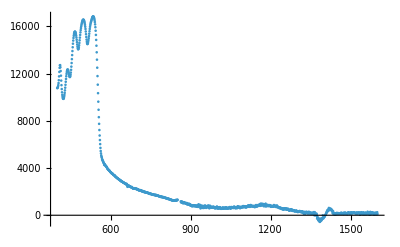

```mathematica
(* row 21 *) 
ktta = datat[[21,4;;]];
ktta2=ktta/.{1.*^-10-> 8*10^(-22)};
ListPlot[plasTTA[ktta2],PlotRange->All]
```

```mathematica
kktatables=Table[ 8*10^(-i),{i,10,21,0.1}];

kktatables2=ktta/.{ktta[[1]]->kktatables[[#]]}&/@Range[Length[kktatables]];

results = plasTTA[#]&/@kktatables2;

(*kttarateimg =ListPlot[results,PlotRange->{{400,600},{0,20000}},Joined->True,AspectRatio->1,Frame->True,ImageSize->Full];
Export["kttarateimg.png",kttarateimg,ImageResolution->500]*)
```

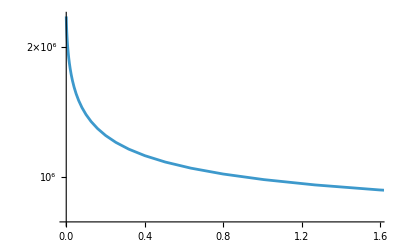

```mathematica
ints = Interpolation[#[[;;-2]]]&/@results;
intsresults = NIntegrate[#[x],{x,400,600}]&/@ints;
ListLogPlot[Transpose[{kktatables,intsresults}],Joined->True]
```

```mathematica
Export["PL_tta_relationship.csv",Transpose[{kktatables,intsresults}]]
```

PL_tta_relationship.csv

```mathematica
Transpose[{kktatables,intsresults}]
```

{{8.×10^-10,691840.+0.183237 ⅈ},{6.35463×10^-10,691855.+0.205596 ⅈ},{5.04766×10^-10,691871.+0.230682 ⅈ},{4.0095×10^-10,691890.+0.258829 ⅈ},{3.18486×10^-10,691911.+0.290411 ⅈ},{2.52982×10^-10,691935.+0.325846 ⅈ},{2.00951×10^-10,691961.+0.365605 ⅈ},{1.59621×10^-10,691991.+0.410215 ⅈ},{1.26791×10^-10,692024.+0.460268 ⅈ},{1.00714×10^-10,692061.+0.516427 ⅈ},{8.×10^-11,692103.+0.579439 ⅈ},{6.35463×10^-11,692150.+0.650139 ⅈ},{5.04766×10^-11,692203.+0.729464 ⅈ},{4.0095×10^-11,692262.+0.818467 ⅈ},{3.18486×10^-11,692329.+0.918327 ⅈ},{2.52982×10^-11,692403.+1.03037 ⅈ},{2.00951×10^-11,692487.+1.15608 ⅈ},{1.59621×10^-11,692581.+1.29712 ⅈ},{1.26791×10^-11,692686.+1.45536 ⅈ},{1.00714×10^-11,692804.+1.6329 ⅈ},{8.×10^-12,692936.+1.83208 ⅈ},{6.35463×10^-12,693085.+2.05555 ⅈ},{5.04766×10^-12,693252.+2.30624 ⅈ},{4.0095×10^-12,693439.+2.58748 ⅈ},{3.18486×10^-12,693648.+2.90296 ⅈ},{2.52982×10^-12,693884.+3.25683 ⅈ},{2.00951×10^-12,694147.+3.65375 ⅈ},{1.59621×10^-12,694443.+4.09889 ⅈ},{1.26791×10^-12,694775.+4.59808 ⅈ},{1.00714×10^-12,695148.+5.15778 ⅈ},{8.×10^-13,695565.+5.78521 ⅈ},{6.35463×10^-13,696034.+6.48841 ⅈ},{5.04766×10^-13,696559.+7.27629 ⅈ},{4.0095×10^-13,697148.+8.15873 ⅈ},{3.18486×10^-13,697808.+9.14659 ⅈ},{2.52982×10^-13,698548.+10.2518 ⅈ},{2.00951×10^-13,699378.+11.4874 ⅈ},{1.59621×10^-13,700308.+12.8673 ⅈ},{1.26791×10^-13,701351.+14.4064 ⅈ},{1.00714×10^-13,702519.+16.1202 ⅈ},{8.×10^-14,703828.+18.0245 ⅈ},{6.35463×10^-14,705295.+20.1343 ⅈ},{5.04766×10^-14,706937.+22.4628 ⅈ},{4.0095×10^-14,708776.+25.0188 ⅈ},{3.18486×10^-14,710836.+27.8034 ⅈ},{2.52982×10^-14,713141.+30.8027 ⅈ},{2.00951×10^-14,715720.+33.9745 ⅈ},{1.59621×10^-14,718604.+37.2134 ⅈ},{1.26791×10^-14,721830.+40.1757 ⅈ},{1.00714×10^-14,725437.+42.6347 ⅈ},{8.×10^-15,729468.+45.2767 ⅈ},{6.35463×10^-15,733970.+48.427 ⅈ},{5.04766×10^-15,738995.+51.3873 ⅈ},{4.0095×10^-15,744602.+54.4684 ⅈ},{3.18486×10^-15,750852.+57.1076 ⅈ},{2.52982×10^-15,757816.+59.2289 ⅈ},{2.00951×10^-15,765569.+62.2289 ⅈ},{1.59621×10^-15,774189.+65.4003 ⅈ},{1.26791×10^-15,783766.+66.5441 ⅈ},{1.00714×10^-15,794392.+63.3858 ⅈ},{8.×10^-16,806174.+49.0928 ⅈ},{6.35463×10^-16,819229.+24.8011 ⅈ},{5.04766×10^-16,833680.+5.96079 ⅈ},{4.0095×10^-16,849630.},{3.18486×10^-16,867194.},{2.52982×10^-16,886502.},{2.00951×10^-16,907683.},{1.59621×10^-16,930866.},{1.26791×10^-16,956174.},{1.00714×10^-16,983723.},{8.×10^-17,1.01362×10^6},{6.35463×10^-17,1.04595×10^6},{5.04766×10^-17,1.08079×10^6},{4.0095×10^-17,1.11817×10^6},{3.18486×10^-17,1.15812×10^6},{2.52982×10^-17,1.20061×10^6},{2.00951×10^-17,1.24558×10^6},{1.59621×10^-17,1.2929×10^6},{1.26791×10^-17,1.34244×10^6},{1.00714×10^-17,1.39396×10^6},{8.×10^-18,1.4472×10^6},{6.35463×10^-18,1.50185×10^6},{5.04766×10^-18,1.55755×10^6},{4.0095×10^-18,1.61387×10^6},{3.18486×10^-18,1.67039×10^6},{2.52982×10^-18,1.72663×10^6},{2.00951×10^-18,1.78212×10^6},{1.59621×10^-18,1.83637×10^6},{1.26791×10^-18,1.88892×10^6},{1.00714×10^-18,1.93933×10^6},{8.×10^-19,1.98722×10^6},{6.35463×10^-19,2.03225×10^6},{5.04766×10^-19,2.07415×10^6},{4.0095×10^-19,2.11272×10^6},{3.18486×10^-19,2.14786×10^6},{2.52982×10^-19,2.17953×10^6},{2.00951×10^-19,2.20775×10^6},{1.59621×10^-19,2.23264×10^6},{1.26791×10^-19,2.25436×10^6},{1.00714×10^-19,2.27313×10^6},{8.×10^-20,2.28918×10^6},{6.35463×10^-20,2.30278×10^6},{5.04766×10^-20,2.31421×10^6},{4.0095×10^-20,2.32374×10^6},{3.18486×10^-20,2.33162×10^6},{2.52982×10^-20,2.3381×10^6},{2.00951×10^-20,2.3434×10^6},{1.59621×10^-20,2.34771×10^6},{1.26791×10^-20,2.3512×10^6},{1.00714×10^-20,2.35402×10^6},{8.×10^-21,2.35629×10^6}}

Transpose::nmtx: The first two levels of {{8.×10^-15,6.35463×10^-15,5.04766×10^-15,4.0095×10^-15,3.18486×10^-15,2.52982×10^-15,2.00951×10^-15,1.59621×10^-15,1.26791×10^-15,1.00714×10^-15,8.×10^-16,6.35463×10^-16,5.04766×10^-16,4.0095×10^-16,«24»,1.26791×10^-18,1.00714×10^-18,8.×10^-19,6.35463×10^-19,5.04766×10^-19,4.0095×10^-19,3.18486×10^-19,2.52982×10^-19,2.00951×10^-19,1.59621×10^-19,1.26791×10^-19,1.00714×10^-19,«11»},{«1»}} cannot be transposed.

ListLogPlot::lpn: {{8.×10^-15,6.35463×10^-15,5.04766×10^-15,4.0095×10^-15,3.18486×10^-15,2.52982×10^-15,2.00951×10^-15,«38»,2.52982×10^-19,2.00951×10^-19,1.59621×10^-19,1.26791×10^-19,1.00714×10^-19,«11»},{«1»}}^T is not a list of numbers or pairs of numbers.

ListLogPlot[Transpose[{{8.×10^-15,6.35463×10^-15,5.04766×10^-15,4.0095×10^-15,3.18486×10^-15,2.52982×10^-15,2.00951×10^-15,1.59621×10^-15,1.26791×10^-15,1.00714×10^-15,8.×10^-16,6.35463×10^-16,5.04766×10^-16,4.0095×10^-16,3.18486×10^-16,2.52982×10^-16,2.00951×10^-16,1.59621×10^-16,1.26791×10^-16,1.00714×10^-16,8.×10^-17,6.35463×10^-17,5.04766×10^-17,4.0095×10^-17,3.18486×10^-17,2.52982×10^-17,2.00951×10^-17,1.59621×10^-17,1.26791×10^-17,1.00714×10^-17,8.×10^-18,6.35463×10^-18,5.04766×10^-18,4.0095×10^-18,3.18486×10^-18,2.52982×10^-18,2.00951×10^-18,1.59621×10^-18,1.26791×10^-18,1.00714×10^-18,8.×10^-19,6.35463×10^-19,5.04766×10^-19,4.0095×10^-19,3.18486×10^-19,2.52982×10^-19,2.00951×10^-19,1.59621×10^-19,1.26791×10^-19,1.00714×10^-19,8.×10^-20,6.35463×10^-20,5.04766×10^-20,4.0095×10^-20,3.18486×10^-20,2.52982×10^-20,2.00951×10^-20,1.59621×10^-20,1.26791×10^-20,1.00714×10^-20,8.×10^-21},{1.4472×10^6,1.50185×10^6,1.55755×10^6,1.61387×10^6,1.67039×10^6,1.72663×10^6,1.78212×10^6,1.83637×10^6,1.88892×10^6,1.93933×10^6,1.98722×10^6,2.03225×10^6,2.07415×10^6,2.11272×10^6,2.14786×10^6,2.17953×10^6,2.20775×10^6,2.23264×10^6,2.25436×10^6,2.27313×10^6,2.28918×10^6,2.30278×10^6,2.31421×10^6,2.32374×10^6,2.33162×10^6,2.3381×10^6,2.3434×10^6,2.34771×10^6,2.3512×10^6,2.35402×10^6,2.35629×10^6,2.35811×10^6,2.35957×10^6,2.36073×10^6,2.36167×10^6,2.36241×10^6,2.363×10^6,2.36347×10^6,2.36385×10^6,2.36415×10^6,2.36439×10^6}}],Joined→True]